```mathematica
graphMadrid = {"9"<->"11","11"<->"8","8"<->"7","7"<->"9","10"<->"11","11"<->"gol","19"<->"7","10"<->"19","19"<->"8","8"<->"7","7"<->"gol","1"<->"4","4"<->"8","8"<->"15","15"<->"8","8"<->"19","19"<->"8","8"<->"7","12"<->"11","1"<->"15","15"<->"19","19"<->"8","8"<->"10","10"<->"12","12"<->"7","7"<->"10","7"<->"12","12"<->"9","9"<->"12","12"<->"10","10"<->"7","7"<->"19","19"<->"15","15"<->"10","10"<->"7","7"<->"9","9"<->"11","7"<->"19","19"<->"15","10"<->"7","7"<->"11","11"<->"9","9"<->"8","8"<->"9","9"<->"19","19"<->"10","10"<->"7","7"<->"gol","11"<->"19","19"<->"8","8"<->"10","10"<->"9","9"<->"7","10"<->"19","19"<->"11","10"<->"11","11"<->"gol","15"<->"19","19"<->"10","10"<->"19","1"<->"15","9"<->"19","19"<->"9","9"<->"11","11"<->"9","9"<->"11","3"<->"12","12"<->"8","8"<->"19","19"<->"8","8"<->"7","7"<->"gol","3"<->"11","11"<->"19","19"<->"9","9"<->"11","4"<->"9","9"<->"10","7"<->"10","10"<->"19","19"<->"gol","9"<->"7","7"<->"10","10"<->"9","9"<->"10","10"<->"19","19"<->"24","24"<->"15","15"<->"9","9"<->"11","11"<->"19","19"<->"7","7"<->"24","24"<->"7","7"<->"9","11"<->"19","19"<->"24","24"<->"11","11"<->"9","9"<->"15","15"<->"11","1"<->"4","4"<->"12","12"<->"10","10"<->"12","12"<->"10"};
GraphPlot3D[Graph[graphMadrid],VertexLabeling->True]
```

-Graphics3D-

```mathematica
graphCali = {"7"<->"30","30"<->"16","16"<->"27","27"<->"5","5"<->"7","7"<->"5","21"<->"27","27"<->"16","7"<->"30","30"<->"5","5"<->"30","30"<->"7","7"<->"21","21"<->"7","7"<->"28","7"<->"5","5"<->"27","27"<->"26","26"<->"30","5"<->"16","4"<->"27","27"<->"21","21"<->"20","20"<->"27","27"<->"7","7"<->"21","21"<->"28","28"<->"27","27"<->"30","30"<->"7","7"<->"5","5"<->"20","20"<->"27","4"<->"20","20"<->"5","5"<->"4","4"<->"7","7"<->"5","30"<->"7","7"<->"30","30"<->"26","26"<->"21","21"<->"5","5"<->"30","4"<->"28","28"<->"7","7"<->"20","21"<->"27","27"<->"20","7"<->"30","30"<->"5","5"<->"21","21"<->"7","7"<->"27","27"<->"5","5"<->"27","27"<->"30","30"<->"20","30"<->"7","7"<->"5","5"<->"7","7"<->"6","6"<->"4","4"<->"30","30"<->"4","4"<->"6","6"<->"21","21"<->"16","16"<->"21","7"<->"30","30"<->"5","5"<->"4","4"<->"5","20"<->"30","30"<->"6","7"<->"21","6"<->"30","12"<->"28","30"<->"7","7"<->"28","28"<->"20","20"<->"8","8"<->"30","30"<->"6","6"<->"7","7"<->"8","8"<->"30","30"<->"7","7"<->"8","8"<->"7","7"<->"30","16"<->"26","26"<->"6","6"<->"30","30"<->"8","8"<->"20","20"<->"8","8"<->"20","30"<->"7","7"<->"8","8"<->"28","28"<->"20","20"<->"8","8"<->"20","20"<->"28","28"<->"6","6"<->"8","8"<->"29","29"<->"gol","6"<->"16","16"<->"4","4"<->"21","21"<->"7","7"<->"29","29"<->"8","7"<->"29","29"<->"8","8"<->"7","7"<->"6"};
```

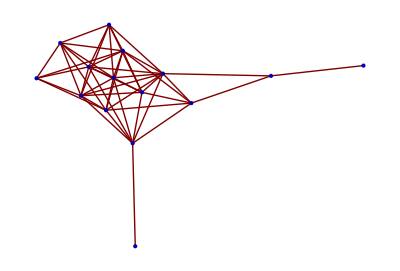

```mathematica
GraphPlot[Graph[graphCali]]
```

```mathematica
Show[%151,ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[%140,ImageSize->Large]
```

-Graphics3D-

```mathematica
VertexDegree[Graph[graphCali]]
```

{43,34,9,19,24,18,12,6,13,19,14,1,19,6,1}

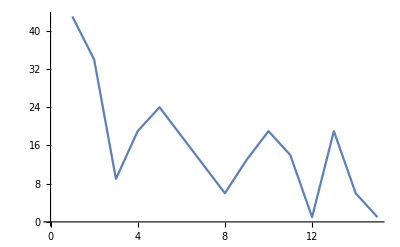

```mathematica
ListLinePlot[{43,34,9,19,24,18,12,6,13,19,14,1,19,6,1}]
```

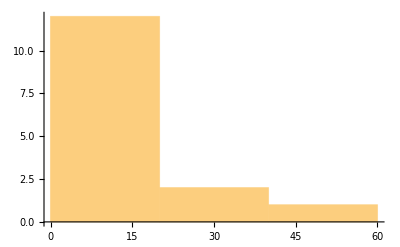

```mathematica
Histogram[{43,34,9,19,24,18,12,6,13,19,14,1,19,6,1}]
```

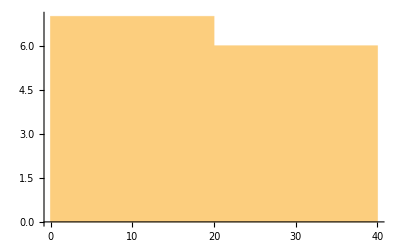

```mathematica
Histogram[{29,24,20,28,28,6,34,4,5,13,13,2,6},2]
```

```mathematica
VertexDegree[Graph[graphMadrid]]
```

{29,24,20,28,28,6,34,4,5,13,13,2,6}

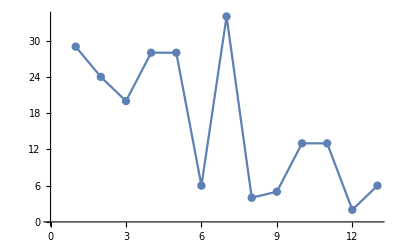

```mathematica
ListLinePlot[{29,24,20,28,28,6,34,4,5,13,13,2,6},Mesh->All]
```

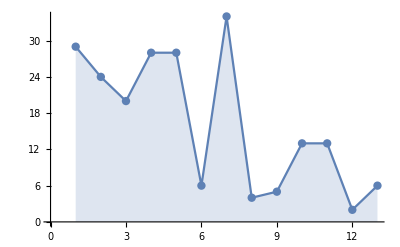

```mathematica
ListLinePlot[{29,24,20,28,28,6,34,4,5,13,13,2,6},Filling->Automatic,Mesh->All]
```

```mathematica
N[MeanGraphDistance[Graph[graphCali]]]
```

1.72381

```mathematica
N[MeanGraphDistance[Graph[graphMadrid]]]
```

1.5641

```mathematica
GlobalClusteringCoefficient[Graph[graphCali]]
```

33/49